```mathematica
Lecture 15: Game Theory
```

Game Theory is the mathematical analysis of conflict and cooperation.

## Learning from experience

### Exercise Subsection

You and Colonel Blotto both have 100 soldiers which are to be distributed to 10 battleﬁelds. Secretly and independently, each commander divides the 100 forces into 10 parts and sends each part to a battleﬁeld. Ten ﬁghts take place, and the larger army wins at each battleﬁeld (neither army wins if the forces are the same size). The ultimate winner is the player who won the most battles. 

For example, if you use the strategy {10,10,10,10,10,10,10,10,10,10} and Colonel Blotto uses the strategy {2,11,11,11,11,11,11,11,11,10}, then Colonel Blotto wins because he won 8 battles to your 1.

a. Write a function named Blotto that inputs two lists of length 10 that sum to 100 (and has a check on the input pattern to make sure that the strategies have this property) and outputs 1 if the first strategy defeats the second, 0 if the strategies tie, and -1 otherwise.

b. The next cell imports a list of 167 blotto strategies submitted by former game theory students.  Each strategy S1 in the list earns a total score by summing the value of Blotto when S1 competes against every other strategy in the list.  Sort the list from the best scoring to the worst scoring.

```mathematica
strategies=Import["/home/tony/Courses/Math350/Spring2024/Blotto.m"]
```

c. Find a strategy that would score higher than all other strategies if it were added to the list of 167 strategies and then the competition in part b was repeated.

```mathematica
Blotto[S1_List/;Length@S1==10&&Total@S1==100,S2_List/;Length@S2==10&&Total@S2==100]:=
Module[{wins=Count[S1-S2,_?Positive],loss=Count[S1-S2,_?Negative]},
Which[wins>loss,1,wins<loss,-1,True,0]]
```

```mathematica
Score[S1_]:=Total[Blotto[S1,#]&/@strategies]
{Score[#],#}&/@SortBy[strategies,Score]//Reverse
```

```mathematica
{Score[#],#}&/@SortBy[Join[strategies,{{7,7,18,8,20,2,8,19,5,6}}],Score]//Reverse
```

### Exercise Subsection

Each one of 100 people select a positive integer.  The winner (if there is one) is the person who selects the smallest number that is not selected by anyone else (see https://en.wikipedia.org/wiki/Unique_bid_auction ).  An optimal strategy is a probability vector {p_1,p_2,p_(3,)...,p_50} such that p_i is the to-be-determined probability that a player selects the integer i. 

Implement this idea to approximate the optimal strategy p:
1. Initialize p to be the vector of length 50 with each entry 1.  This will mean that every number 1 through 50 is equally likely to be selected.
2. Create a list L of 100 random integers between 1 and 50 with probability weighted using p (use RandomChoice[p->Range@n]).  This L models 100 people playing the game.
3. Select the smallest number in L that is not repeated, say it is m.
4. Update p by adding 1 position m in p.
5. Repeat steps 2 through 4 many times.  The approximate optimal strategy is the probability vector p/Total@p.

### Exercise Subsection

A random permutation of 1,2,...,n is selected.  

The strategy is as follows: Automatically reject the first r candidates for some r.  Then, take the next number that is the largest seen so far, possibly resulting in not selecting a number.

```mathematica
InitallyReject[L_,r_]:=Module[{candidates=Select[L[[r+1;;]],#>Max@L[[;;r]]&]},candidates!={}&&First@candidates==Max@L]
```

```mathematica
L=RandomSample@Range@10
```

{3,9,2,8,1,4,10,5,6,7}

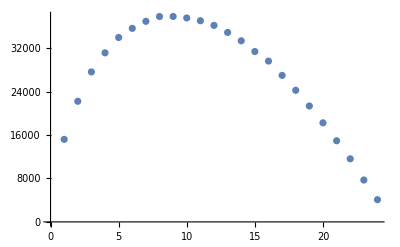

```mathematica
ListPlot[Sort@Tally@Flatten@Table[Flatten@Position[InitallyReject[RandomSample@Range@25,#]&/@Range@25,True],100000]]
```

## Matrix Games

A matrix game on a matrix A has two players: a row player and a column player.  The row player secretly selects a row r, the column player secretly selects a column c.  When choices are revealed, the row player earns A[[r,c]] from the column player.  Therefore the row player wants to maximize A[[r,c]] and the column player wants to minimize A[[r,c]].

For example, the matrix in the next cell models “rock, paper, scissors” with the winner earning $1 from the loser.

```mathematica
A={{0,-1,1},{1,0,-1},{-1,1,0}};
TableForm[A,TableHeadings->{{"Rock","Paper","Scissors"},{"Rock","Paper","Scissors"}}]
```

| Rock | Paper | Scissors
Rock | 0 | -1 | 1
Paper | 1 | 0 | -1
Scissors | -1 | 1 | 0

An optimal strategy for the row (or column) player is a probability vector that gives the probability that a rational and intelligent player should play each row.  Finding optimal row and column strategies can be found using the code in the next cell.

```mathematica
RowStrategy[P_]:=Module[{d=Dimensions@P,L},(L=LinearProgramming[Table[1,d[[1]]],Transpose@P+1-Min@P,Table[1,d[[2]]]])/Total@L]
ColStrategy[P_]:=RowStrategy@Transpose[-P]
```

For example, for the “rock, paper, scissors” matrix A defined above, the next cell gives the (somewhat obvious) optimal strategies for the row and column player:

```mathematica
RowStrategy@A
ColStrategy@A
```

{1/3,1/3,1/3}

{1/3,1/3,1/3}

### Exercise Subsection

There are occasionally penalty kicks in soccer. Each penalty kick involves only a kicker and a goalie.  1417 actual penalty kicks in professional soccer matches were analyzed to arrive at this matrix game, where the kicker is the row player, the goalie is the column player, and the entries give the probability of a goal.

```mathematica
soccer={{.58,.95},{.93,.7}};
TableForm[soccer,TableHeadings->{{"Kick right","Kick left"},{"Anticipate right","Anticipate left"}}]
```

| Anticipate right | Anticipate left
Kick right | 0.58 | 0.95
Kick left | 0.93 | 0.7

Give the optimal strategies for the kicker and the goalie.

### Exercise Subsection

Morra is a hand game.

### Exercise Subsection

Rose secretly writes down 1, 2, or 3. Colin repeatedly guesses Rose' s number until guessing correctly.  After an incorrect guess of k, Rose tells Colin if his guess is higher or lower than k . At the end of the game, Colin pays Rose the number of guesses it took to ﬁnd Rose' s secret number. Solve using the simplex algorithm.

### Exercise Subsection

A random integer r between 1 and 100 is selected.  Two players both try to guess r, and the player that is closest without going over is the winner (like the Price is Right game show). 

a. Write a function named Payoff[i_,j_,r_] that has input the guess i for the first player, the guess j for the second player, the integer r between 1 and 100.  The output should be 1 if the first player wins, -1 if the second player wins, and 0 if there is a tie or neither player wins.

```mathematica
Payoff[i_,j_,r_]:=Which[i==j,0,r<Min[{i,j}],0,i<=r<j,1,i<j<=r,-1,j<=r<i,-1,j<i<=r,1]
```

b.  Once the function Payoff has been defined, then the expected payoff matrix A can be defined with the code in the next cell:

```mathematica
ExpectedPayoff[i_,j_]:=Sum[Payoff[i,j,r]/100,{r,100}]
A=Table[N@ExpectedPayoff[i,j],{i,100},{j,100}];
```

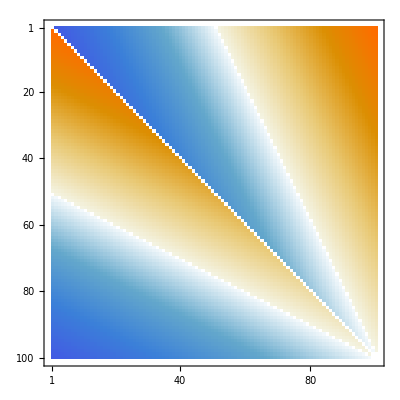

-1+10/(√(100-x))

```mathematica
A//MatrixPlot
F[x_]:=Which[x<=0,0,x>3/4,1,True,1/Sqrt[1-x]-1]
y[x]/.First@DSolve[{0==(2x−200)y'[x]+1+y[x],y[0]==0},y,x]//Simplify
```

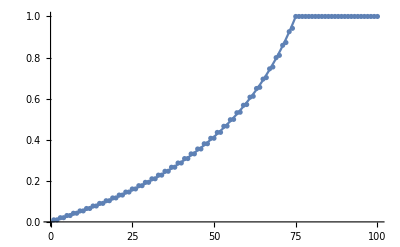

```mathematica
Show[ListPlot[Accumulate[First@GameSolution@N@A//Chop]],Plot[-1+10/(√(100-x)),{x,0,75}]]
```

### Exercise Subsection

fictitious play

## Nonzero sum games

### Exercise Subsection

The prisoner’s dilemma is a two player game

### Exercise Subsection

Chicken is a two player game

## The Shapley value and voting